# QMeSTools Showcase

## Load Package

```mathematica
(* Load the installed version of the package *)
Needs["QMeSderivation`"]
```

## Define the theory (a QCD truncation)

```mathematica
fRGEq = {
"Prefactor"->{1/2},
<|"type"->"Regulatordot", "indices"->{i,j}|>,
<|"type"->"Propagator", "indices"->{i,j}|>
};

fieldsQCD=<|
"bosonic"-> {
σ[p],(*sigma meson*)
Π[p,{a}],(*pions*)
 A[p,{v, c}](*gluon*)
},
 "fermionic"->{
{sb[p,{d,c}],s[p,{d,c}]},(*strange quark*)
{qb[p,{d,c,f}],q[p,{d,c,f}]},(*light quarks*)
{cb[p,{c}],c[p,{c}]}(*ghosts*)
}
|>;

TruncationQCD = {
{σ,σ},{Π,Π},{q,qb},{s,sb},{A,A},{c,cb},(* propagators *)
{qb,q,A},{cb,c,A},{sb,s,A},{A,A,A},{A,A,A,A},(* gluon sector scatterings *)
{qb,q,σ},{qb,q,Π},{qb,q,σ,σ},{qb,q,Π,Π},{qb,q,σ,Π},{qb,q,σ,σ,σ},{qb,q,σ,σ,Π},{qb,q,σ,Π,Π},{qb,q,Π,Π,Π}, (* quark-meson scatterings *)
 {σ,σ,σ},{σ,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π},{Π,Π,Π,Π}(* meson scatterings *)
};

SetupfRGQCD= <|"MasterEquation"->fRGEq,
"FieldSpace"->fieldsQCD,
"Truncation"->TruncationQCD
|>;
```

## FRG Equations

### Derive flow equation of four-quark vertex

```mathematica
DerivativeListqbqqbq= {qb[p,{d4,c4,f4}],q[q,{d3,c3,f3}],qb[-p,{d2,c2,f2}],q[-q,{d1,c1,f1}]};
Diagramsqbqqbq=DeriveFunctionalEquation[SetupfRGQCD,DerivativeListqbqqbq,"OutputLevel"->"SuperindexDiagrams"];
Diagramsqbqqbq//Length
```

400

### Reduce the number of diagrams by using the symmetries of the tensor structure and the t-channel configuration

```mathematica
ReduceIdenticalFlowDiagrams::usage
```

ReduceIdenticalFlowDiagrams[diagrams,symmetries]

Reduce a set of flow equations by matching identical topologies and/or by utilizing a given set of symmetries.

```mathematica
symmetries={
{
{qb,{p,{d4,c4,f4}}}->{qb,{-p,{d2,c2,f2}}},
{qb,{-p,{d2,c2,f2}}}->{qb,{p,{d4,c4,f4}}},
{q,{q,{d3,c3,f3}}}->{q,{-q,{d1,c1,f1}}},
{q,{-q,{d1,c1,f1}}}->{q,{q,{d3,c3,f3}}}
},
{
{qb,{p,{d4,c4,f4}}}->{qb,{-p,{d2,c2,f2}}},
{qb,{-p,{d2,c2,f2}}}->{qb,{p,{d4,c4,f4}}}
},
{
{q,{q,{d3,c3,f3}}}->{q,{-q,{d1,c1,f1}}},
{q,{-q,{d1,c1,f1}}}->{q,{q,{d3,c3,f3}}}
}
};
DiagramsqbqqbqReduced=ReduceIdenticalFlowDiagrams[Diagramsqbqqbq,symmetries];
DiagramsqbqqbqReduced//Length
```

61

### Plot the resulting diagrams

```mathematica
PlotSuperindexDiagram::usage
```

PlotSuperindexDiagram[diagram, setup, options]

Plot a single superindex diagram. The first argument to this function is the diagram itself, the second one is a valid QMeS setup.
The diagram has to be a superindex diagram.

The options for the function PlotSuperindexDiagram are:
"ShowEdgeLabels" ->  False / True
	This option will toggle whether edges are plotted together with labels to identify them.
"EdgeStyle" ->  List
	Using this option, one can specify the edge styles of different propagators. e.g.,
		"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}}
	may produce a diagram like
	{-1/2,Graph[{{$CellContext`externalLeg$155993$156004}, {$CellContext`externalLeg$155993$156007}, {$CellContext`externalLeg$155993$156010}, {$CellContext`externalLeg$155993$156013}, {$CellContext`i}, {$CellContext`a83$471882}, {$CellContext`a83$471893}, {$CellContext`a83$471910}, {$CellContext`a83$471979}}, {{{6, 5}, {8, 7}, {2, 8}, {4, 6}, {5, 9}, {7, 3}, {9, 1}}, {{6, 7}, {8, 9}}}, {FormatType -> TraditionalForm, EdgeStyle -> {UndirectedEdge[{$CellContext`a83$471910}, {$CellContext`a83$471979}] -> {RGBColor[1, 0.5, 0]}, DirectedEdge[{$CellContext`a83$471882}, {$CellContext`i}] -> {RGBColor[0, 0, 1]}, UndirectedEdge[{$CellContext`a83$471882}, {$CellContext`a83$471893}] -> {{Dashing[{Small, Small}], Thickness[Large]}}, DirectedEdge[{$CellContext`i}, {$CellContext`a83$471979}] -> {RGBColor[0, 0, 1]}, DirectedEdge[{$CellContext`externalLeg$155993$156013}, {$CellContext`a83$471882}] -> {RGBColor[0, 0, 1]}, DirectedEdge[{$CellContext`a83$471979}, {$CellContext`externalLeg$155993$156004}] -> {RGBColor[0, 0, 1]}, DirectedEdge[{$CellContext`a83$471910}, {$CellContext`a83$471893}] -> {RGBColor[0, 0, 1]}, DirectedEdge[{$CellContext`a83$471893}, {$CellContext`externalLeg$155993$156010}] -> {RGBColor[0, 0, 1]}, DirectedEdge[{$CellContext`externalLeg$155993$156007}, {$CellContext`a83$471910}] -> {RGBColor[0, 0, 1]}}, VertexLabels -> {{$CellContext`externalLeg$155993$156010} -> $CellContext`qb, {$CellContext`externalLeg$155993$156004} -> $CellContext`qb, {$CellContext`externalLeg$155993$156007} -> $CellContext`q, {$CellContext`externalLeg$155993$156013} -> $CellContext`q}, VertexShape -> {{$CellContext`i} -> Graphics[{Thickness[Large], Line[{{2^Rational[-1, 2], 2^Rational[-1, 2]}, {-2^Rational[-1, 2], -2^Rational[-1, 2]}}], Line[{{2^Rational[-1, 2], -2^Rational[-1, 2]}, {-2^Rational[-1, 2], 2^Rational[-1, 2]}}], Circle[{0, 0}, 1]}]}, VertexSize -> {{$CellContext`i} -> Medium}}]}

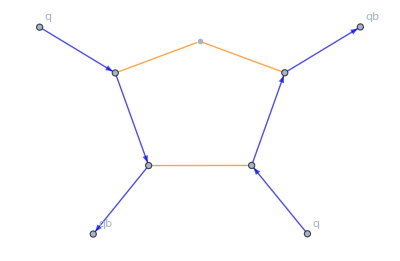
{4,-Graphics-}

```mathematica
PlotSuperindexDiagram[
DiagramsqbqqbqReduced[[1]],SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```

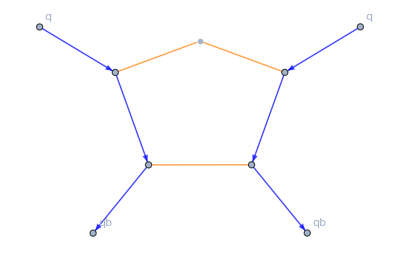
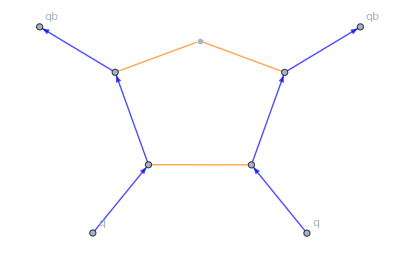
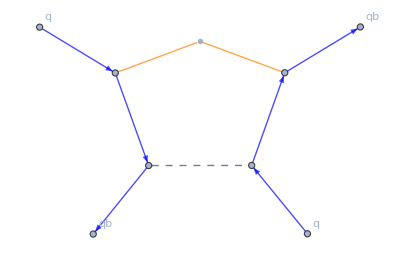
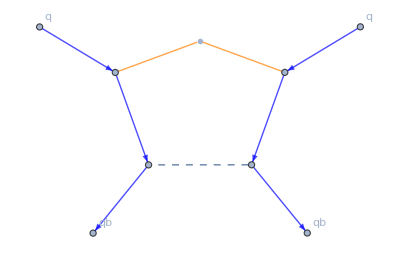
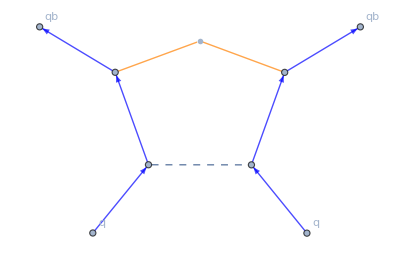
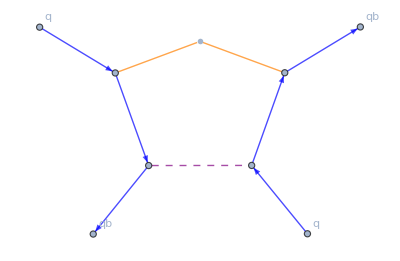
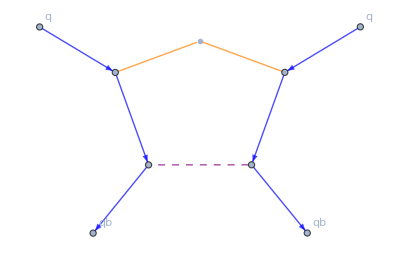
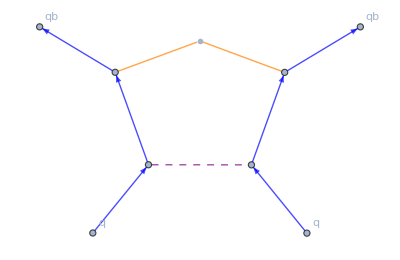
{{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{2,-Graphics-},{-2,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-4,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-},{-2,-Graphics-}}

```mathematica
PlotSuperindexDiagrams[
DiagramsqbqqbqReduced,SetupfRGQCD,
"EdgeStyle"->{q->Blue,A->Orange,Π->{Dashed,Thick},σ->{Dashed,Thick,Purple}},
"ShowEdgeLabels"->False
]
```